```mathematica
(*2. Считать данные из полученного входного файла в системе Wolfram Mathematica (учесть, что размерность графа может быть любой и параметры bi могут идти в произвольном порядке).*)
```

```mathematica
inFileName=StringJoin[NotebookDirectory[],"input.txt"];
fileStream=OpenRead[inFileName];
Is=Read[fileStream,{Word,Number}][[2]];
Us=Read[fileStream,{Word,Number}][[2]];
U=ReadList[fileStream,Expression,Us];
b=ReadList[fileStream,String,Is];
b=Sort[Table[StringSplit[b[[i]],{"b","_","/*","*/ ", " "}], {i,Is}]];
UDirect=Table[U[[i,1]]->U[[i,2]],{i,Us}]
Close[fileStream];
```

{1->2,3->1,1->4,5->2,1->6,3->6,3->7,4->3,5->3,5->6,6->2,7->1,7->4}

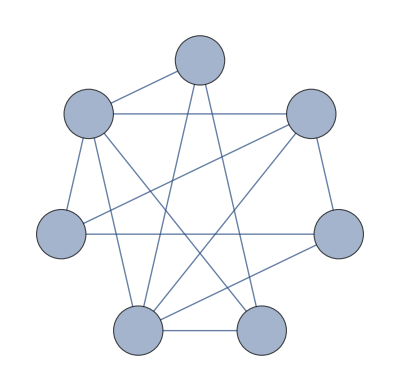

```mathematica
(*3. По полученным данным создать ориентированный граф с заданием стилей/*)
g = Graph[UDirect, GraphLayout->"CircularEmbedding", VertexLabels->Placed["Name",Center], VertexSize->0.4, VertexLabelStyle-> Directive[Italic, 28], EdgeShapeFunction->GraphElementData["FilledArrow","ArrowSize"->0.05], EdgeStyle->Thick]
```

```mathematica
(*3. Построить списковые структуры хранения корневого дерева (список узлов, список предков, список направлений, список глубин узлов, список связи или династического обхода;корень дерева-узел, от которого строили покрывающее дерево, либо любой произвольный узел.*)
pred=ConstantArray[0,Is];(*список предков*)
dir=ConstantArray[0,Is];(*список направлений*)
depth=ConstantArray[0,Is]; (*список глубин узлов*)
dinast=ConstantArray[0,Is];(*династичесий обход*)
posl={};                                            (*последовательность обхода*)
RootTree={};                                   (*корневое дерево*)
Ut={};                                               (*покрывающее дерево*)
root=1;
ug=UndirectedGraph[g];
DepthFirstScan[ug,root,{"FrontierEdge"->Function[edge,{
pred[[edge[[2]]]]=edge[[1]],
depth[[edge[[2]]]]=depth[[edge[[1]]]] + 1,
{i=edge[[1]]->edge[[2]],AppendTo[RootTree,i],If[MemberQ[UDirect,i],{AppendTo[Ut,i],dir[[edge[[2]]]]=1},{AppendTo[Ut,edge[[2]]->edge[[1]]],dir[[edge[[2]]]]=-1}]}
}],
"PrevisitVertex"->Function[vertex,{If[posl≠{},dinast[[posl[[-1]]]]=vertex],AppendTo[posl,vertex]}]
}];
dinast[[posl[[-1]]]]=root;
(*Print[Range[Is]];
Print[pred];
Print[depth];
Print[dir];
Print[dinast];
Print[posl];*)
```

## Лабораторная 5.

```mathematica
fileName=FileNameJoin[{NotebookDirectory[],"Lab_5.pdf"}];
img=Image[Graph[g,GraphHighlight->EdgeList[Ut],GraphLayout->"CircularEmbedding",EdgeStyle->Thick, VertexLabels->Placed["Name",Center], VertexSize->0.4,VertexLabelStyle-> Directive[Italic, 28]]];
nb2=CreateDocument[]
NotebookWrite[nb2,Cell["Граф:","Text"]];
NotebookWrite[nb2,ToBoxes[img]];
SelectionMove[nb2,Next,Cell];
```

a8v2f_shm33FrontEndObject[LinkObject["a8v2f_shm", 3, 1]]33Untitled-8

```mathematica
(* 1. Написать функцию построения частного решения системы уравнений баланса (в функциональном стиле);*) 
edges=Subscript[x,#]&/@UDirect;
h[]:=Block[{result},
xp=ConstantArray[0,Is];
result=ConstantArray[0,Us];
complement=Complement[UDirect,Ut];
reverse=Reverse[posl];
xp=Fold[With[{i=#2,j=-dir[[#2]]*ToExpression[b[[#2]][[2]]]}, ReplacePart[#1,{i->#1[[i]]+j,pred[[i]]->#1[[pred[[i]]]]+dir[[i]]*dir[[pred[[i]]]]*(#1[[i]]+j)}]]&,xp,Take[reverse,Is-1]];
f[i_,j_]:=Return[0]/;MemberQ[complement,i->j];
f[i_,j_]:=Return[xp[[j]]]/;MemberQ[RootTree,i->j];
f[i_,j_]:=Return[xp[[i]]]/;MemberQ[RootTree,j->i];
result=Table[edges[[n]]==f[edges[[n]][[2]][[1]],edges[[n]][[2]][[2]]],{n,1,Us}]]
```

```mathematica
(* 2. Найти и вывести частное решение для своей системы уравнений,проверить правильность найденного решения путём подстановки решения в систему (Solve).*)
r=h[]
s=Solve[r]
s=Simplify[r/.s[[1]]]
NotebookWrite[nb2,Cell["Частное решение:","Text"]];
NotebookWrite[nb2,ToBoxes[r]];
SelectionMove[nb2,Next,Cell];
NotebookWrite[nb2,Cell["Проверка решения:","Text"]];
NotebookWrite[nb2,ToBoxes[s]];
Export[fileName,nb2];
```

{x_(1->2)==0,x_(3->1)==-2,x_(1->4)==0,x_(5->2)==3,x_(1->6)==0,x_(3->6)==0,x_(3->7)==0,x_(4->3)==2,x_(5->3)==0,x_(5->6)==0,x_(6->2)==3,x_(7->1)==0,x_(7->4)==3}

{{x_(1->2)→0,x_(1->4)→0,x_(1->6)→0,x_(3->1)→-2,x_(3->6)→0,x_(3->7)→0,x_(4->3)→2,x_(5->2)→3,x_(5->3)→0,x_(5->6)→0,x_(6->2)→3,x_(7->1)→0,x_(7->4)→3}}

{True,True,True,True,True,True,True,True,True,True,True,True,True}